```mathematica
(* Initialization *)
QCTMC=QueueInit[4,1,"A"];
GovME=GovernMat[QCTMC];
NumM=N[GovME];
initstate=Flatten[RandomInitState[QCTMC,"A"]];
```

```mathematica
(*Running time - Linearly - from t = 1 to t = 1000 *)
SSTimeLinear=List[];
PadeTimeLinear=List[];
KryTimeLinear=List[];
SSErrorLinear=List[];
PadeErrorLinear=List[];
KryErrorLinear=List[];
Do[
t=i;
ssRes=AbsoluteTiming[ExpSS[NumM*t]];
PadeRes=AbsoluteTiming[MatrixExp[NumM*t,Method->"Pade"]];
KryRes=AbsoluteTiming[MatrixExp[NumM*t,N[initstate],Method->"Krylov"]];
item1={t,ssRes[[1]]};
item2={t,PadeRes[[1]]};
item3={t,KryRes[[1]]};
AppendTo[SSTimeLinear,item1];
AppendTo[PadeTimeLinear,item2];
AppendTo[KryTimeLinear,item3];
If[i≤Power[2,7],
ExaRes=MatrixExp[GovME*t];
ExaInitRes=ExaRes.initstate;
AppendTo[SSErrorLinear,Max[Abs[ssRes[[2]]-ExaRes]]];
AppendTo[PadeErrorLinear,Max[Abs[PadeRes[[2]]-ExaRes]]];
AppendTo[KryErrorLinear,Max[Abs[KryRes[[2]]-ExaInitRes]]];];
If[Mod[i-1,100]==0,Print[i];];
,{i,1,900,10}];
```

1

101

201

301

401

501

601

701

801

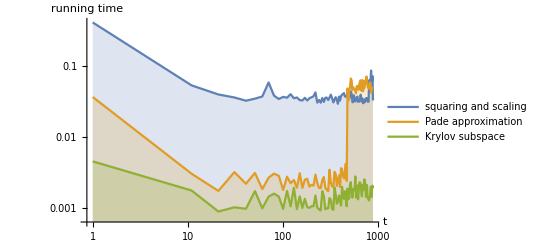

```mathematica
ListLinePlot[{SSTimeLinear,PadeTimeLinear,KryTimeLinear},Filling->Axis,PlotLegends->{"squaring and scaling","Pade approximation","Krylov subspace"},AxesLabel->{"t","running time"},ScalingFunctions->{"Log","Log"}]
```

```mathematica
(*Running Time - Exponentially*)
SSTimeExp=List[];
PadeTimeExp=List[];
KryTimeExp=List[];
SSErrorExp=List[];
PadeErrorExp=List[];
KryErrorExp=List[];
Do[
i=1;
(*t=Power[2,i];*)
ssRes=AbsoluteTiming[ExpSS[NumM*t]];
PadeRes=AbsoluteTiming[MatrixExp[NumM*t,Method->"Pade"]];
KryRes=AbsoluteTiming[MatrixExp[NumM*t,N[initstate],Method->"Krylov"]];
AppendTo[SSTimeExp,ssRes[[1]]];
AppendTo[PadeTimeExp,PadeRes[[1]]];
AppendTo[KryTimeExp,KryRes[[1]]];
If[i≤7,
ExaRes=MatrixExp[GovME*t];
ExaInitRes=MatrixExp[GovME*t,initstate];
ssError=Max[Abs[ssRes[[2]]-ExaRes]];
PadeError=Max[Abs[PadeRes[[2]]-ExaRes]];
KryError=Max[Abs[KryRes[[2]]-ExaInitRes]];
AppendTo[SSErrorExp,ssError];
AppendTo[PadeErrorExp,PadeError];
AppendTo[KryErrorExp,KryError];
];
,{t,1,50}];
```

```mathematica
KryError=Max[Abs[KryRes[[2]]-ExaInitRes]]
```

5.2805×10^-15

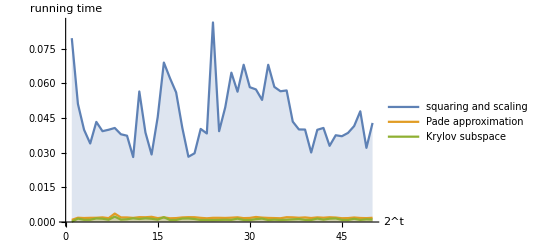

```mathematica
OverallTimeTime=ListLinePlot[{SSTimeExp,PadeTimeExp,KryTimeExp},Filling->Axis,PlotLegends->{"squaring and scaling","Pade approximation","Krylov subspace"},AxesLabel->{"2^t","running time"}]
```

```mathematica
Export[NotebookDirectory[]<>"EPS_figure\\OverallTimeTime.eps",OverallTimeTime]
```

C:\Users\mei\Desktop\Transient Analysiso of QCTMC\Code\EPS_figure\OverallTimeTime.eps

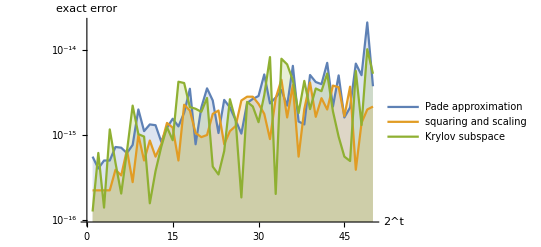

```mathematica
OverallTimeAcu=ListLinePlot[{SSErrorExp,PadeErrorExp,KryErrorExp},Filling->Axis,PlotLegends->{"Pade approximation","squaring and scaling","Krylov subspace"},AxesLabel->{"2^t","exact error"},ScalingFunctions->"Log"]
```

```mathematica
Export[NotebookDirectory[]<>"EPS_figure\\OverallTimeAcu.eps",OverallTimeAcu]
```

C:\Users\mei\Desktop\Transient Analysiso of QCTMC\Code\EPS_figure\OverallTimeAcu.eps

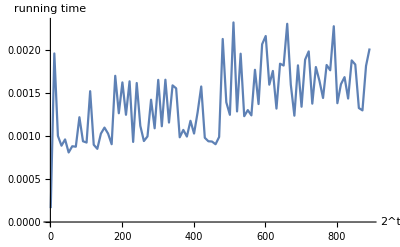

```mathematica
ListLinePlot[KryTimeLinear,AxesLabel->{"2^t", "running time"}]
```

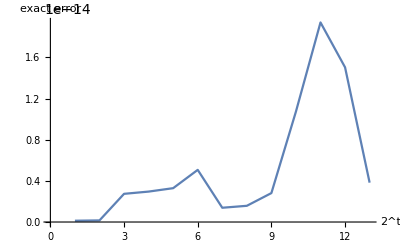

```mathematica
ListLinePlot[KryErrorLinear,AxesLabel->{"2^t", "exact error"}]
```

```mathematica
ExaRes=MatrixExp[GovME];
```

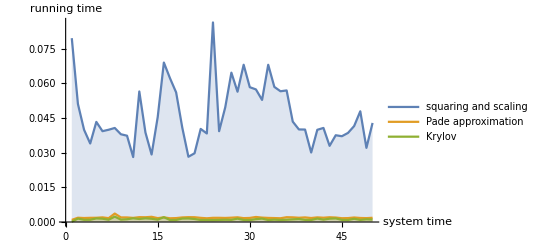

```mathematica
ListLinePlot[{SSTimeExp,PadeTimeExp,KryTimeExp},Filling->Axis,PlotLegends->{"squaring and scaling","Pade approximation","Krylov"},AxesLabel->{"system time","running time"}]
```

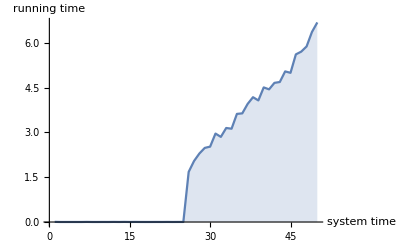

```mathematica
ListLinePlot[KryTimeExp,Filling->Axis,AxesLabel->{"system time","running time"}]
```

```mathematica
KryTimeExp
```

{0.00526324,0.000848152,0.000836978,0.000891733,0.000761549,0.00081407,0.00354347,0.000835581,0.000803733,0.00176028,0.00120434,0.00346329,0.00140884,0.00406309,0.00116858,0.00328031,0.00136051,0.00108757,0.00114735,0.00196226,0.0012429,0.0028336,0.00123116,0.00235002,0.00208071,1.67836,2.04198,2.29316,2.48009,2.52233,2.95955,2.84886,3.14621,3.12249,3.61797,3.63619,3.95203,4.17664,4.06933,4.50412,4.43961,4.65675,4.6852,5.03994,4.99277,5.61015,5.70178,5.87536,6.35921,6.67907}